# Gradient Descent

Aaron Lopes

## Backstory

### Mathematical Motivation

```mathematica
WordDefinition["gradient"]
```

{the property possessed by a line or surface that departs from the horizontal,a graded change in the magnitude of some physical quantity or dimension}

In mathematics, the term gradient holds several definitions. Most generally, it is interchangeable with slope, describing the rate of change of a function. In multivariate and vector calculus, it describes the direction in which the steepest upward rate of change occurs within a function. This can be found by taking the derivative of the function with respect to (w.r.t) its independent variables.

```mathematica
{Slider[Dynamic[a],{-5,5}],Dynamic[a]}
```

{,}

```mathematica
{Slider[Dynamic[b],{-5,5}],Dynamic[b]}
```

{,}

The sliders above will allow you to change the horizontal and vertical steepness of the quadric surface below, also known as a hyperbolic paraboloid. The darker the hue, the more dramatic the ascent or descent.

```mathematica
Clear[g,grad]
```

```mathematica
g[a_,b_][x_,y_] := (x/a)^2-(y/b)^2
```

```mathematica
Dynamic[Plot3D[ g[a,b][x,y],{x,-5,5},{y,-5,5},ColorFunction->Hue]]
```

Below, we will perform our calculations on our function of two variables, which will provide us with our gradient vector .

```mathematica
grad := Grad[g[a,b][x,y], {x,y}];
Dynamic[grad]
```

We see that, depending on the chosen values for a and b, the plotted vector points toward the direction of steepest ascent.

```mathematica
Dynamic[With[{field = grad},VectorPlot[field, {x, -5, 5}, {y,-5,5},StreamPoints->Coarse, StreamColorFunction->Hue]]]
```

Conversely, the negative gradient represents the direction of steepest descent.

```mathematica
Dynamic[With[{field = -grad},VectorPlot[field, {x, -5, 5}, {y,-5,5},StreamPoints->Coarse, StreamColorFunction->Hue]]]
```

### Application to Machine Learning

The method of gradient descent as a minimizer for nonlinear functions was first introduced by the French mathematician Augustin-Louis Cauchy,

```mathematica
WebImageSearch["Augustin-Louis Cauchy", "Images"][[1]]
```

-Graphics-

whose work was motivated by the mechanics of astronomical bodies. In his work to solve for the orbit of these various bodies, he devised a method of optimization in equation solving. He considered a function u=f(x,y,z,...) which stayed continuous and never became negative. In order to find the values x,y,z,... satisfying the equation u=0, the function u would be continuously decreased  “until it vanishe[d]”.

If we let X=f'_x, Y=f'_y, Z=f'_z...be the derivatives w.r.t. the independent variables. If we let θ >0 and  
	Θ = f(x-θ X, y-θ Y,z-θ Z, ...)
Θ will become smaller than u if θ is of a smaller size. If we increase the value of θ, then the value Θ of υ will eventually vanish, or coincide with a minima of the function υ. This can be expressed as 
	Θ'_θ  = 0
 This Gradient Method optimization method was essentially the “alpha” version of our newly improved methods of Gradient Descent, such as Stochastic Gradient Descent and Stochastic Approximation.

## Learning Example with Gradient Descent

Suppose we have a dataset which spans 6 years, which represents the number of people infected with Tuberculosis, starting in 2001 and going to 2006. We can see that our plotted data represents somewhat of an upwards trend, so our line of best fit should reflect this trend.

```mathematica
SeedRandom[]
```

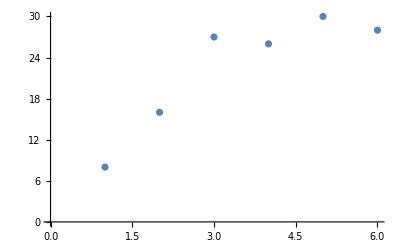

```mathematica
data ={{1,8},{2,16},{3,27},{4,26},{5,30},{6,28}};
ts = TimeSeries[data];
ListPlot[ts]
```

In order to build our regression model, we will first generate two random values, a and b, which will represent the slope of our line and the y-intercept, respectively. In order to properly structure of time-value matrix, we will transpose it to create two separate columns.

```mathematica
Clear[ypred,yp,sse,totalsse,grada,gradb,totalgrada,totalgradb,a,b]
```

```mathematica
xa = Transpose[data][[1]];
```

```mathematica
ya = Transpose[data][[2]];
weightsab = RandomReal[{5,10},{2}];
```

After looking at the plotted data, we can estimate that the slope of our line will be somewhere between 5 and 10, so we will generate our random weights to be within this range.

```mathematica
a = weightsab[[1]];
b= weightsab[[2]];
{a,b}
```

{8.62174,9.77374}

```mathematica
predict[a_, b_, x_] := a + b * x;
```

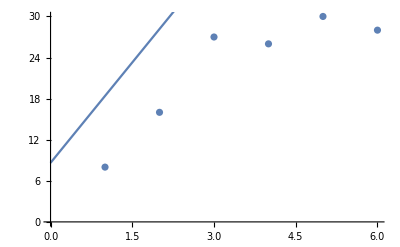

```mathematica
Show[ListPlot[ts],Plot[a+b*x,{x,0,6}]]
```

Comparing our regression line to our plotted data, we see that it is nowhere close to providing an accurate prediction for our data. In order to fine tune our parameters, we will begin our method of learning by gradient descent.

```mathematica
yp = predict[a,b,xa];
```

```mathematica
sse[yactual_, ypred_] := Total[1/2*(yactual-ypred)^2];
grada[yactual_, ypred_] := Total[-(yactual-ypred)];
gradb[yactual_,ypred_,xactual_] := Total[-(yactual- ypred) * xactual];
```

We have made three important computations which provide us with information on our current random prediction, and on how to improve our current prediction. The first is the sum of our mean squared error. This calculation gives us a quantitative idea of how accurate our current prediction is. The higher the error, the less accurate our model. The following two calculations are the sum of all the gradients for our mean squared error function w.r.t. the two parameters we are attempting fine-tune, a and b.

```mathematica
sumsquarederror = sse[ya,yp]
```

1572.46

```mathematica
totalgrada = grada[ya,yp]
```

121.979

```mathematica
totalgradb = gradb[ya,yp,xa]
```

527.467

Before we adjust our a and b values, let’s take a look at where our random values lie on the mean squared error plot. We can see that although our initial guess was close to minima of the plot, it is far from accurate. The gradients provide us with a general direction to step towards, but it is up to us to chose a reasonable step size. If the step size is too large, we risk the possibility of overshooting our minimization. If the step size is too small, it will take us exponentially more computing time to reach our minimum. For this case, let’s choose a step size of 0.01.

```mathematica
s[X_,Y_,a_,b_ ] := 1/2*(Y-(a+b*X))^2 ;
```

```mathematica
Show[Plot3D[s[x,y,a,b],{x,-40.0,40.0},{y,-40.0,40.0},ColorFunction->Hue],Graphics3D[{Black,PointSize[0.05],Point[{a,b,sumsquarederror}]}]]
```

-Graphics3D-

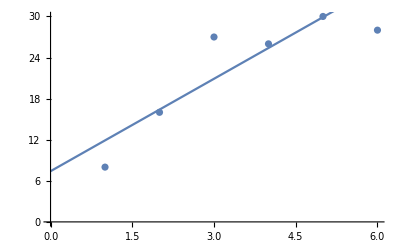

```mathematica
a=  a- 0.01*totalgrada;
b = b - 0.01*totalgradb;
Show[ListPlot[ts],Plot[a+b*x,{x,0,6}]]
```

With only one iteration of training, we can see that our method of gradient descent has been highly effective in adjusting our regression parameters. This line provides a much better fit for our data, but we must also keep in mind that the size of our data to begin with was fairly small. With larger datasets, it would require many more iterations to provide a better fit. After using these updated parameters in our model, we can see that the sum of our mean squared error has also dramatically decreased.

```mathematica
yp = predict[a,b,xa];
sumsquarederror = sse[ya,yp]
```

46.9423

## Training the Model for Accuracy

In order to further increase the accuracy of our model, we will need to take several more steps towards our minima. However, it is important to consider how many steps we want to take in total. In our first iteration of training, we saw that our total error dramatically decreased and our model become far more accurate. This will not be the case in future iterations. The initial step size we chose of 0.01 works well for the first round of iteration due to the dataset being somewhat smaller, but because the regression parameters have been so heavily adjusted, it will now be a slow creep towards reaching our minima. If you continue to evaluate the code above, starting from the initial prediction, this pattern will be reflected.